## OLD

```mathematica
Manipulate[
Plot[ -Abs[KK y+Ybounce],{y,-30,30},PlotRange->{-30,30},AxesLabel->{"Y","X"}],

{KK,-2,2,.01},
{Ybounce,0,15}
]
```

## NO

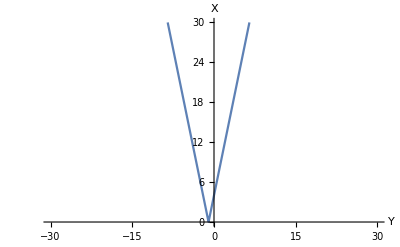

```mathematica
Plot[2Abs[2y+2],{y,-30,30}, PlotRange->{0,30}, AxesLabel->{"Y","X"}]
```

```mathematica
Manipulate[
Plot[(y2-y1)/(x2-x1)(x-x1)+y1,{x,0,30},PlotRange->{0,30}],
{x1,6,30},
{y1,2,30},
{x2,0,30},
{y2,0,30}
]
```

## Left Wall LG

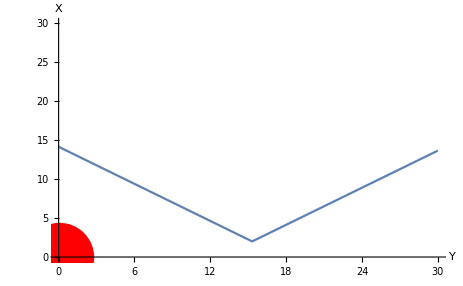

9.3834

```mathematica
x1=10;
y1=2.7;
x2=8.75+2.5;
y2=29.5;

k=(x1+x2)/(y2-y1);
yo=x1/(x1+x2)(y2-y1)+y1;
Co=-k yo;
x[y_]:=Abs[k y +Co]+2
p2=Graphics[{Red,PointSize[.13],Point[{0,0}]}];
p1=Plot[x[y],{y,0,30}, AxesLabel->{"Y","X"}, PlotRange->{0,30}];
Show[p1,p2]
x[6]
```

```mathematica
x[10]
```

0

## Right Wall

16.5323

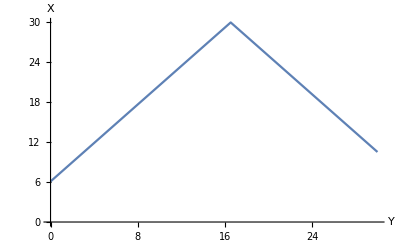

```mathematica
L=30;
k2=(2 L-x1-x2)/(y2-y1);
yo2=((L-x1)(y2-y1))/(2 L -x1-x2)+y1
Co2=-k2 yo2;
xx[y_]:= L-Abs[k2 y+Co2]
Plot[xx[y],{y,0,30}, AxesLabel->{"Y","X"}, PlotRange->{0,30}]
```

## Straight

10.8682

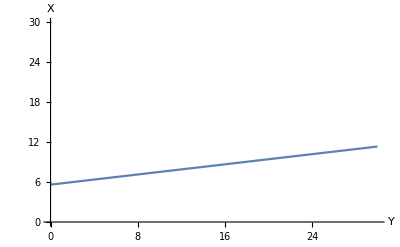

```mathematica
XS[y_]:=(y-y1)/((y2-y1)/(x2-x1))+x1
XS[27.5]
Plot[XS[y],{y,0,30}, AxesLabel->{"Y","X"}, PlotRange->{0,30}]
```

```mathematica
√(12.59/π)
```

2.00188

```mathematica
deg=90/82.
44/deg
```

1.09756

40.0889

```mathematica
173-254
173-90
```

-81

83

```mathematica
4.8 Sin[46 Degree]
4.8-4.8 Cos[38 Degree]+1
```

3.45283

2.01755